Corso di Laboratorio Computazionale, Corso di Laurea in Matematica,  Università di Padova.        
A.A. 2023-2024

# Esercizi 3: Frattali classici

Notebook del gruppo: coppiaSpagnola

Componenti del gruppo: Paula Frutos Romo e Germán Gil Planes

Se ci sono state collaborazioni e/o aiuti al di fuori del gruppo, dichiararli:
In collaborazione con: 
Aiutato da:

Consegna entro:  16/04

## Esercizio 3.1: Guarnizione di Sierpinski

## Testo dell’esercizio

### Testo dell’esercizio

Esercizio 3.1

1) Disegnare le approssimazioni della guarnizione di Sierpinski, illustrata nella seguente figura:

2) Mettere in evidenza la autosimilarità

#### Suggerimenti ed osservazioni:

- Lavorare su liste di triangoli, con triangolo=lista dei suoi tre vertici.
- La funzione da iterare rende un triangolo e ne restituisce 3. Basta scrivere i vertici di questi 3 triangoli in funzione dei vertici di quello iniziale.
- La primitiva grafica “triangolo pieno” si chiama   Polygon[{vertici}]

Per evidenziare la autosimilarità utilizzare una finestrella ed opportuni ingradimenti di opportune parti.

## Soluzione

```mathematica
(*Definizione di funzioni*)
guar1[vertici_]:={{vertici[[1]],1/2(vertici[[1]]+vertici[[2]]),1/2(vertici[[1]]+vertici[[3]])},{1/2(vertici[[1]]+vertici[[2]]),vertici[[2]],1/2(vertici[[2]]+vertici[[3]])},{1/2(vertici[[1]]+vertici[[3]]),1/2(vertici[[2]]+vertici[[3]]),vertici[[3]]}}

guar2[vertici_]:=Flatten[guar1/@vertici,1]
guar3[vertici_,n_]:=Nest[guar2, vertici,n]//N
guar[vertici_,n_]:=Graphics[Polygon[guar3[vertici,n]]]//N
```

```mathematica
(*Finestrella e autosimilirità (3,4). Ogni triangolo è diviso in quattro triangoli,di cui tre rimangono. Quindi, m=3 e k=4. Vediamo una finestra con un sottotriangolo, dove possiamo vedere come si forma la divisione.*)
finestra[gr_,{x1_,x2_,y1_,y2_}]:=Show[gr,Graphics[{Red,Line[{{x1,y1},{x2,y1},{x2,y2},{x1,y2},{x1,y1}}]}]]
triangoloIniciale={{{0,0},{1,0},{0.5,(√3)/2}}};
finestrella=finestra[guar[triangoloIniciale,5],{.24,.51,.42,.66}]
```

```mathematica
(*Grafici finali*)
guarnizione=GraphicsRow[Table[Show@guar[triangoloIniciale,s],{s,0,5}],Background->LightBlue,ImageSize->800]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["finestrella.jpg",finestrella];
Export["Esercizio1.jpg",guarnizione];
Run["finestrella.jpg"];
Run["Esercizio1.jpg"];
```

## Esercizio 3.2: Tappeto di Sierpinski

## Testo dell’esercizio

### Testo dell’esercizio

Esercizio 3.2 Disegnare le approssimazioni del Sierpinski carpet, illustrato nella seguente figura:


egnare le approssimazioni del tappeto di Sierpinski

#### Suggerimenti ed osservazioni:

Suggerimenti:
- lavorare su liste di quadrati, con quadrati = lista dei suoi 4 vertici.
- La funzione da iterare prende un quadrato e ne restituisce 8. Conviene farla così:
     - si fa una Table (automaticamente, con il comando Table) che crea i 9 quadrati ottenuti dividendo i lati del quadrato in tre:
                        Table[{p1+m e1+n e2,.....},{m,0,2},{n,0,2}],
       ove e1 ed e2 sono i vettori della base standard di R^2.
     - si butta via quello centrale (Delete[lista, {posizione}])
- La primitiva grafica “quadrato pieno” si chiama   Polygon[{vertici}]

PS: Non creare la lista degli otto quadrati a mano: il codice è illeggibile, e non è generalizzabile alla spugna di Menger.

## Soluzione

```mathematica
(*Definizione di funzioni*)
(*lunghezza del quadrato piccolo*)
l[vertici_]:=(vertici[[3,1]]-vertici[[1,1]])/3

tap1[vertici_]:=Module[{elems,flattened},
e1={1,0}l[vertici];
e2={0,1}l[vertici];elems=Table[{vertici[[1]]+p e1 +q e2 ,vertici[[1]]+(p+1)e1 +q e2 ,vertici[[1]]+(p+1)e1 +(q+1)e2,vertici[[1]]+p e1 +(q+1)e2 },{p,0,2},{q,0,2}];
flattened=Flatten[elems,1];
Delete[flattened,{5}]]

tap2[vertici_]:=Flatten[tap1/@vertici,1]
tap3[vertici_,n_]:=Nest[tap2, vertici,n]//N
tap[vertici_,n_]:=Graphics[Polygon[tap3[vertici,n]]]//N
```

```mathematica
(*Grafici finali*)
quadratoIniciale={{{0,0},{1,0},{1,1},{0,1}}};
tappeto=GraphicsRow[Table[Show@tap[quadratoIniciale,s],{s,0,5}],Background->LightBlue,ImageSize->800]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Esercizio2.jpg",tappeto];
Run["Esercizio2.jpg"];
```

## Esercizio 3.3: Spugna di Menger

## Testo dell’esercizio

### Testo dell’esercizio

Disegnare le approssimazioni della spugna di Menger mostrata nella seguente figura:

### Suggerimenti ed osservazioni:

Suggerimenti:
- procedere come nel caso precedente.
- La primitiva grafica è ora “cuboid”; naturalmente serve Graphics3D, non Graphics.

- Attenzione: i file sono piuttosto grossi e il rendering lento già per n=4. Salvare il notebook prima di fare le figure.

C’è anche un’altra possibile implementazione, che crea tables più piccole, ma non si guadagna in velocità:  ’idea è di lavorare solo con il vertice in basso a sinistra e con il lato del quadrato, invece che con tutti e quattro i vertici

## Soluzione

```mathematica
(*Definizione di funzioni*)
(*lunghezza del lato del cubo piccolo*)
k[vertici_]:=(vertici[[2,1]]-vertici[[1,1]])/3

spu1[vertici_]:=Module[{elems,flattened},
e1={1,0,0}k[vertici];
e2={0,1,0}k[vertici];
e3={0,0,1}k[vertici];elems=Table[{vertici[[1]]+p e1 +q e2 +r e3,vertici[[1]]+(p+1)e1+(q+1)e2+(r+1)e3},{p,0,2},{q,0,2},{r,0,2}];
flattened=Flatten[elems,2];
Delete[flattened,{{5},{11},{13},{14},{15},{17},{23}}]]

spu2[vertici_]:=Flatten[spu1/@vertici,1]
spu3[vertici_,n_]:=Nest[spu2, vertici,n]//N
spu[vertici_,n_]:=Graphics3D[Cuboid@@@spu3[vertici,n]]//N
```

```mathematica
(*Grafici finali*)
cuboIniciale={{{0,0,0},{1,1,1}}};
spugna=GraphicsRow[Table[Show@spu[cuboIniciale,s],{s,0,3}],Background->LightBlue,ImageSize->800]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Esercizio3.jpg",spugna];
Run["Esercizio3.jpg"];
```

## Esercizio 3.4: L-sistemi

## Testo dell’esercizio

### Testo dell’esercizio

Esercizio 1
Creare una funzione 
      turtle[ nit_, str_, rrule_, angolo_]
che, per ogni numero di iterazioni (nit), stringa iniziale (str) nell’alfabeto {F,+,-}, regola di riscrittura (rrule) e angolo di rotazione (angolo) produce il disegno del cammino della tartaruga. 

Provarla su un esempio.

### Suggerimenti ed osservazioni:

- Se possibile, fare in modo caso che la stringa iniziale sia scritta con i caratteri (F,+,-). 
- Si può usare un Module.
- Decidete voi se definire le funzioni F,p,m all’esterno (più veloce?) o all’interno del Module.
- L’argomento rrule che specifica la rewriting rule può essere passato come stringa  (per es, “FpFm” per la rewriting rule  F→FpFm).
- Volendo si possono aggiungere degli argomenti alla funzione turtle per specificare l’ImageSize o altro. Può essere utile prevedere che tali argomenti siano opzionali. Vedere “Optional and Default Arguments” sull’Help.

## Soluzione

```mathematica
(*Definizione di funzioni*)
ToLst[stringa_]:=Map[Symbol,Characters[stringa]];
path[ListaFunz_]:=ComposeList[ListaFunz,{{0,0.},{1.,0}}];
first[lista_]:=Map[First,path[lista]];
drawpath[ListaConfig_,size_]:=Graphics[Line@first@ListaConfig,ImageSize->size];
(*In generale nella programmazione, in termini di velocità,non cambia molto se le funzioni vengono dichiarate all'interno o all'esterno del modulo. Per comodità e leggibilità, dichiariamo all'interno le funzioni che dipendono direttamente o indirettamente da qualche argomento.*)

(*Funzione chiedata*)
turtle[nit_,str_,rrule_,angolo_,size_]:=Module[{R,Rinv,strIniziale,rule},
strIniziale=StringReplace[str,{"+"->"p","-"->"m"}];
Switch[Head[rrule],String,rule=F->ToLst@rrule,List,rule=F->rrule,Rule,rule=rrule];
RRLst[lst_]:=Flatten[lst/.rule];
RRLst[lista_,n_]:=Nest[RRLst,lista,n];
R=Chop@RotationMatrix[angolo];
Rinv=Chop@Inverse[R];
F[{x_,v_}]:={x+v,v};
p[{x_,v_}]:={x,R.v};
m[{x_,v_}]:={x,Rinv.v};

drawpath[RRLst[ToLst@strIniziale,nit],size]
]
```

```mathematica
(*Esempi della lezione*)
```

```mathematica
Esempio1=turtle[3,"F","FpFmmFpF",Pi/3.,500]
```

```mathematica
(*Con i simboli '-' invece'm'*)
Esempio2=turtle[4,"F--F--F","FpFmmFpF",Pi/3.,300]
```

```mathematica
Esempio3=turtle[3,"F","FmFpFpFpFmFmFmFpF",Pi/2.,400]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Esercizio4_Esempio1.jpg",Esempio1];
Export["Esercizio4_Esempio2.jpg",Esempio2];
Export["Esercizio4_Esempio3.jpg",Esempio3];
Run["Esercizio4_Esempio1.jpg"];
Run["Esercizio4_Esempio2.jpg"];
Run["Esercizio4_Esempio3.jpg"];
```

## Esercizio 3.5: Paesaggi frattali e dimensione box-counting

## Testo dell’esercizio

### Testo dell’esercizio

a) Costruire un (bel) paesaggio frattale.

b) Determinare la dimensione del “box-counting” di qualche paesaggio costruito con diversi valori dell’esponente α  del fattore di riscalamento k=2^α della variazione casuale delle altezze.

c) Si riesce a formulare un’ipotesi sulla dipendenza della dimensione box-counting dall’esponente α? [Questo è laborioso. Non è obbligatorio farlo, ma se ci riuscite è molto apprezzato]

#### Suggerimenti ed osservazioni:

Per b), evidenziate su qualche esempio che la  dimensione box-counting dipende da α.

Naturalmente la dimensione che rileverete dipenderà un po’ dal numero di iterazioni che fate nella costruzione del paesaggio frattale, come illustrato dai seguenti grafici log-log della funzione j →M_j relativi a tre diversi valori del numero di iterazioni.

Per c), confrontate i fit relativi allo stesso numero di iterazioni e due o più diversi valori di α e provate a vedere se si comprende la dipendenza da α.

## Soluzione

```mathematica
(*Definizione di funzioni del paesaggio*)
pmedio[{a_,b_},{r_,α_},n_]:={a,(a+b)/2+2^(-α n)r RandomReal[{-1,1}]}
riga[lst_,{r_,α_},n_]:=Append[Flatten[Map[pmedio[#,{r,α},n]&,Partition[lst,2,1]]],Last[lst]]
f[matr_,rα_,n_]:=Transpose[Map[riga[#,rα,n]&, Transpose[Map[riga[#,rα,n]&,matr]]]]
f2[matr_,rα_,nit_]:=Fold[f[#1,rα,#2]&,matr,Range[nit]]
f3[matr_,rα_,sealevel_,nit_]:=Map[Max[#,sealevel]&,f2[matr,rα,nit],{2}]

(*Una iterazione extra per variare anche il mare e generare l'onde*)
f4[matr_,rα_,sealevel_,nit_]:=f3[f3[matr,rα,sealevel,nit],{0.005,0.5},sealevel,1]

combinareColori[cf1_,cf2_,cf3_]:=Function[{x,y,z},Which[z<0.015,cf1[z],0.015<=z<0.5,cf2[z],z>=0.5,cf3[z]]];
fig[matr_,rα_,sealevel_,nit_]:=ListPlot3D[f4[matr,rα,sealevel,nit],Mesh->None,Boxed->False,Axes->False,PlotRange->All,ColorFunction->combinareColori[ColorData["Aquamarine"],ColorData["GreenBrownTerrain"],Blend[{White,LightBlue},#]&]]
matrran[dim_]:=RandomReal[{-1,1},{dim,dim}]

(*Definizione di funzioni per box-counting*)
M[F_,j_]:= Length@Union@Floor[j F]
fit[F_,j1_,j2_,p_]:=Fit[Table[{Log@j,Log@M[F,j]},{j,j1,j2,p}],{1,x},x]
BC[F1_,F2_,F3_,j1_,j2_,p_]:=ListLogLogPlot[{Table[{j,M[F1,j]},{j,j1,j2,p}],Table[{j,M[F2,j]},{j,j1,j2,p}],Table[{j,M[F3,j]},{j,j1,j2,p}]},PlotRange->{{j1,j2},All},PlotLegends->{"α1=0.01","α2=0.2","α3=0.5"},PlotStyle->PointSize[Small]]
```

```mathematica
(* Apartato a): Disegno del paesaggio *)
(*Questa è la matrice del nostro paesaggio. Se vuoi ussare questa oppure genera un'altra nuova nella prossima istruzione.*)
m={{-0.17715800245579993,0.4679501388651839,0.43267433542163003,0.8727120474360479},{0.8794166236207053,-0.7490233175800576,0.36178352157984905,-0.6109829948723688},{-0.6360184904804038,0.632737299502661,-0.8798485779968717,0.7016578760473382},{-0.5403968987017582,0.32854739056787663,0.03491312179297923,-0.37830978618671907}};
```

```mathematica
m=matrran[4]
```

```mathematica
paesaggio=fig[m,{.1,.5},0,6]
```

-Graphics3D-

```mathematica
(*Abbiamo salvato m per tutti i casi di diversi alfa*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Paesaggio.jpg",paesaggio];
Run["Paesaggio.jpg"];
```

```mathematica
(* Apartato b): box-counting *)
(*Nella lezione si ha detto che 0<=alfa<=0.5. Prendiamo alfa in {0.01,0.2,0.5}*)
(*Fissamo r=0.75, perché, dopo aver effettuato delle prove, abbiamo notato che quanto più grande è r tanto più significativi sono i cambiamenti. *)

(*CASO 1: alfa=0.01*)
paesaggioBC=f3[m,{.75,.01},0,6];
Dimensions[paesaggioBC]
```

{193,193}

```mathematica
(*Per simplificare, mappamo a un solo vettore come nel caso della lezione. Facciamo lo stesso per tutti i valori di alfa. Quindi, non condiziona l'analisi.*)
p1=Map[List,Flatten@paesaggioBC];
Dimensions[p1]
```

{37249,1}

```mathematica
(*CASO 2: alfa=0.2*)
paesaggioBC=f3[m,{.75,0.2},0,6];
p2=Map[List,Flatten@paesaggioBC];
```

```mathematica
(*CASO 3: alfa=0.5*)
paesaggioBC=f3[m,{.75,0.5},0,6];
p3=Map[List,Flatten@paesaggioBC];
```

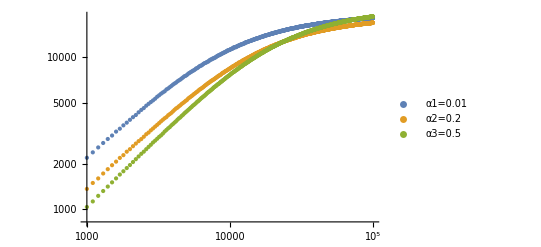

```mathematica
graficoAlfaDiversi=BC[p1,p2,p3,1000,100000,100]
```

```mathematica
Export["Esercizio5Grafico.jpg",graficoAlfaDiversi];
Run["Esercizio5Grafico.jpg"];
```

```mathematica
(*Apartato c)*)
(* Maggiore è l'alfa, minore è il fattore di scala e quindi abbiamo osservato nel grafico che, generalmente, maggiore è la dimensione di Haussdorf.

Diciamo "generalmente" perché stiamo lavorando con variazioni casuali che potrebbero rendere ciò non vero in determinate occasioni. Tuttavia,abbiamo effettuato sufficienti test e siamo giunti empiricamente a questa conclusione. Inoltre,abbiamo osservato che più alto è l'alfa, meno brusco appare il paesaggio. *)

fit[p1,1000,100000,100]
fit[p2,1000,100000,100]
fit[p3,1000,100000,100]
```

6.45559+0.301058 x

5.28495+0.398596 x

4.39074+0.486172 x

```mathematica
(* 
 Guardando l'output dei fit di sopra, vediamo i coeficienti...
Dimension frattale 1 --> 0.2959646701497356 (alfa=0.01)
Dimension frattale 2 --> 0.39700721016589835 (alfa=0.2)
Dimension frattale 3 --> 0.5526482056817817 (alfa=0.5)

Ovviamente questi valori possono variare in diversi provi perché stiamo lavoriando con variazioni casuali.
*)
```